15

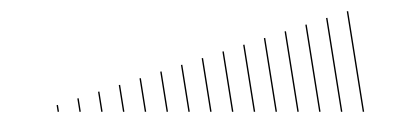

```mathematica
length=10;
rotation=π/10;
breaks=15
(* Lets make evenly spaced lined *)
Graphics[Table[Line[{r*length*{Cos[rotation],Sin[rotation]},
				{length*r,0}}],{r,0,1,1/breaks}]]
```

```mathematica
Clear [HalfPart]

(* Now we get the coordinates of these points and randomly connect them using polygon function in wolfram *)

HalfPart [ breaks_,length_, rotation_,connection_:Polygon]:=
Block[{lines},
lines= Table[Line[{r*length*{Cos[rotation],Sin[rotation]},
				{length*r,0}}],{r,0,1,1/breaks}];
Join[connection@RandomSample[
Flatten[lines/.Line[{x_,y_}]:>{x,y},1]]]];
```

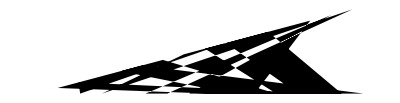

```mathematica
show1=HalfPart[15,15,π/12];
Graphics[show1]
```

```mathematica
Clear [FullPart]

(* Now we use reflection transform tomake an image that we can duplicate n number of times *)
FullPart[temp_]:=
{temp,GeometricTransformation[temp,ReflectionTransform[{0,1}]]};
```

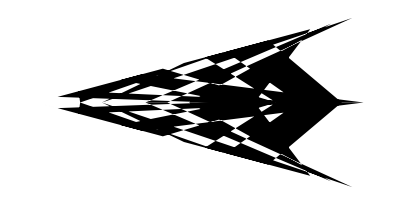

```mathematica
show2=FullPart[show1];
Graphics[show2]
```

```mathematica
(* From the docs - Rotation Matrix gives the 2D rotation matrix that rotates 2D vectors counterclockwise byθradians. *)

Graphics[GeometricTransformation[show2,Table[RotationMatrix[a],{a,0,2 π- rotation,rotation}]]]
```

-Graphics-

```mathematica
(* Now I will wrap it in a function in which values can be manipulated later*)
```

```mathematica
MandalaFull[breaks_,length_, rotation_,connection_:Polygon]:=
Block[{oneSegment},
oneSegment= FullPart[
HalfPart[breaks,length, rotation]];
GeometricTransformation[oneSegment,
Table[RotationMatrix[a],
{a,0,2 π- rotation,rotation}]]];
```

```mathematica
(* Now i wil make all the parameters customizble to make new mandalas on the fly *)
Manipulate[
Graphics[
MandalaFull[numbreaks,numlength,π/numrotation,connectionfunc]],
{numbreaks,2,50,1},
{numlength,5,20,1},
{numrotation,2,30,1},
{connectionfunc,{Polygon,BezierCurve,Line}}];
```

```mathematica
Manipulate[Graphics[MandalaFull[numbreaks,numlength,π/numrotation,connectionfunc]],{numbreaks,2,50,1},{numlength,5,20,1},{numrotation,2,30,1},{connectionfunc,{Polygon,BezierCurve,Line}}]
```

```mathematica
Manipulate[Graphics[MandalaFull[numbreaks,numlength,numrotation,connectionfunc]],{numbreaks,2,50,1},{numlength,5,20,1},{numrotation,π/170,π/2,π/180},{connectionfunc,{Polygon,BezierCurve,Line}}]
```

```mathematica
loc4=CreateDirectory["mandala03"]
```

C:\Users\kunal_bem86lt\Documents\mandala03

```mathematica
Table[
Export[
FileNameJoin[
{loc4,StringJoin["mandala",ToString[numbreaks],ToString[N[numrotation,5]],ToString[connectionfunc],".jpg"]}],
Graphics[
MandalaFull[numbreaks,10,π/numrotation,connectionfunc]]],
{numbreaks,5,30,1},
{numrotation,2,20},
{connectionfunc,{Polygon,BezierCurve,Line}}];
```

```mathematica
CloudDeploy[
Manipulate[
Graphics[
MandalaFull[numbreaks,numlength,π/numrotation,connectionfunc]],
{numbreaks,2,50,1},
{numlength,5,20,1},
{numrotation,2,30,1},
{connectionfunc,{Polygon,BezierCurve,Line}}],
Permissions->"Public"];
```

```mathematica
CloudObject["https://www.wolframcloud.com/obj/a1eb70b1-2f4f-4270-9cf6-b93747d4b276"]
```

CloudObject[https://www.wolframcloud.com/obj/a1eb70b1-2f4f-4270-9cf6-b93747d4b276]